```mathematica
"Consider the function f(x)=x^4-24x^2+12x on[-5,5].Sketch the graph of f' and f" over the stated interval,then use those graph to estimate the x corordinates of the inflection points of f,the intervals on which f is concave up or down ,and the intervals on which f is increasing or decreasing."
```

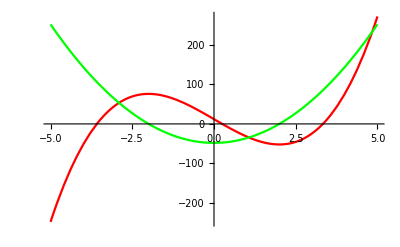

```mathematica
f[x_]=x^4-24*x^2+12*x;
df1=D[f[x],x];
df2=D[f[x],{x,2}];
Plot[{df1,df2},{x,-5,5},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]}]
```

```mathematica
b
```

```mathematica
96+9
```

⁃Graphics⁃

```mathematica
Plot[f[x],{x,-5,5}]
```

⁃Graphics⁃

```mathematica
NSolve[df1==0]
```

{{x→-3.58292},{x→0.251323},{x→3.3316}}

```mathematica
df1/.{x->-5}
```

-248

```mathematica
(*f is decreasing on -5 to -3.58292*)
```

```mathematica
df1/.{x->-2}
```

76

```mathematica
(*f is increasing on -3.58292 to 0.251323*)
```

```mathematica
df1/.{x->2}
```

-52

```mathematica
(*f is decreasing on 0.251323 to 3.3316*)
```

```mathematica
df1/.{x->4}
```

76

```mathematica
(*f is decreasing on  3.3316 to 5*)
```

```mathematica
NSolve[df2==0]
```

{{x→-2.},{x→2.}}

```mathematica
(*Point of inflection is -2 and 2*
```

```mathematica
df2/.{x->-4}
```

144

```mathematica
(* f is concave up-5 to -2*)
```

```mathematica
df2/.{x->-1}
```

-36

```mathematica
(* f is concave down from -2 to 2*)
```

```mathematica
df2/.{x->3}
```

60

```mathematica
(* f is concave up from  2 to 5*)
```